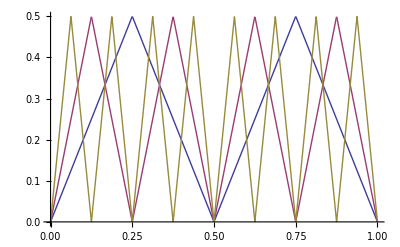

```mathematica
f[x_]:=Piecewise[{{2x,x<0.25},{(1-2x),x<0.5},{2(x-0.5),x<0.75},{1-2(x-0.5),x<1}}]
Plot[{f[x],f[f[x]],f[f[f[x]]]},{x,0,1}]
```

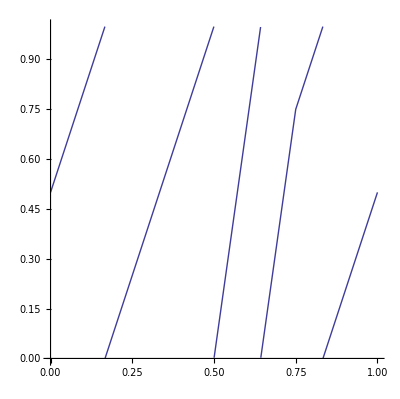

```mathematica
f[x_]:= Mod[2 Abs[x-0.5]-2Abs[x-0.75]+3x,1]
Plot[f[x],{x,0,1}, AspectRatio -> Automatic]
```

rotation number doesn' t make sense for 2 - 1

rotation number is well-defined for *homeomorphisms* from the circle to itself.

1.

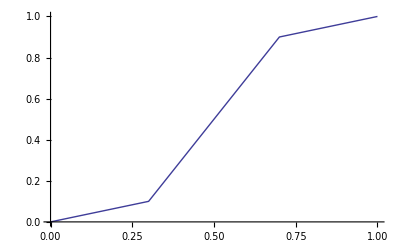

```mathematica
h[x_]:=(x+(Abs[x-0.3]-Abs[x-0.7])/0.4 +1)/3
h[1]
Plot[h[x],{x,0,1}]
```

arXiv:0811.2800 Parallel Chip-Firing on the Complete Graph: Devil’s Staircase and Poincare Rotation Number. Lionel Levine. math.CO 
(see theorem 8 works for any staircase)

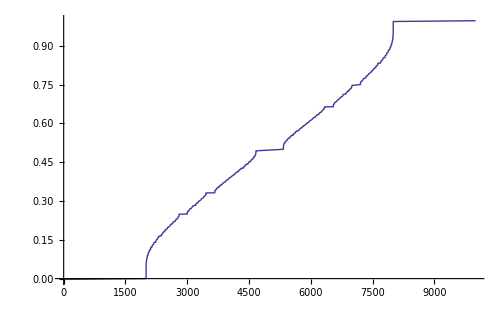

```mathematica
Clear[g,h]
h[x_]:=(x+(Abs[x-0.3]-Abs[x-0.7])/0.4 +1)/3
g[x_]:=h[Mod[x,1]]+Floor[x]
graph = Plot[g[x],{x,0,2}];
n=100;
(*iterations =  Plot[Table[Nest[g,x,k],{k,1,n}],{x,0,1}];
rotation = Plot[Table[(Nest[g,x,k]-x)/k,{k,1,n}],{x,0,1}];
GraphicsRow[{graph,iterations,  rotation}]*)
ListPlot[Table[(Nest[(g[#]+b)&,0.3,n]-0.3)/n,{b,0,1,0.0001}], Joined -> True]
```

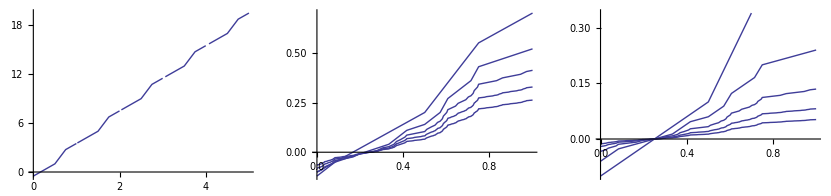

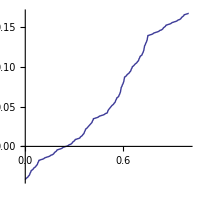

```mathematica
Clear[g,h]
h[x_]:=2 Abs[x-0.5]-2Abs[x-0.75]+3x
g[x_]:=h[Mod[x,1]]+Floor[x]*(h[1]-h[0])
graph = Plot[g[x],{x,0,5}];
n=5;
iterations =  Plot[Table[Nest[g,x,k]/5^k,{k,1,n}],{x,0,1}, AspectRatio -> 1];
rotation = Plot[Table[(Nest[g,x,k]-x)/k/5^k,{k,1,n}],{x,0,1}];
GraphicsRow[{graph,iterations,  rotation}]
n=7;
 Plot[Nest[g,x,n]/5^n,{x,0,1}, AspectRatio -> 1]
```

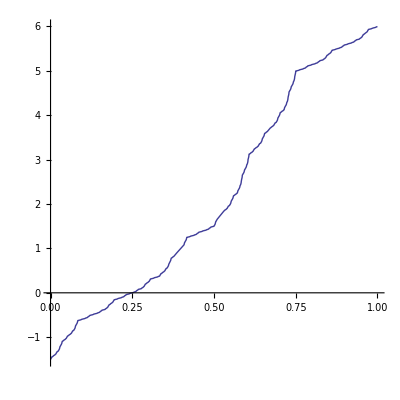

```mathematica
Plot[Nest[g,x,n]/3^n,{x,0,1}, AspectRatio -> 1]
```